## Physics shit

### Function that simply determines the size of the basis based on the StateList

```mathematica
Basiscount[StateList_]:=(TOTALBASIS = {};For[i=1,i<Dimensions[StateList][[1]]+1,i++,TOTALBASIS=Append[TOTALBASIS,2*StateList[[i,3]]+1]];
x=Total[TOTALBASIS])
```

### Function that Generates the basis vectors indexed by relevant quantum numbers

```mathematica
(*Psi[n,j,l,F,mf]*)
PSIBASISGEN[StateList_,basdim_]:=(count=1;For[i=1,i<Dimensions[StateList][[1]]+1,i++,For[j=-StateList[[i,3]],j<(StateList[[i,3]]+1),j++,PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]=UnitVector[basdim,count];count+= 1]])
```

### Function that determines the coupling coefficients

```mathematica
(*Try flipping...*)
(*CouplingConstant[JJ_,LL_,FF_,MFF_,J_,L_,F_,MF_,I_,d_,q_]:=If[Abs[LL-L]== 1,d*(-1)^(1+I+JJ+F)*√((2F+1)(2JJ+1))*SixJSymbol[{J,I,F},{FF,1,JJ}]*ClebschGordan[{F,MF},{1,q},{FF,MFF}],0]*)
CouplingConstant[JJ_,LL_,FF_,MFF_,J_,L_,F_,MF_,I_,d_,q_]:=1

(*(*Try flipping...*)
CouplingConstant[JJ_,LL_,FF_,MFF_,J_,L_,F_,MF_,I_,d_,q_]:=If[Abs[LL-L]== 1,d*(-1)^(1+I+JJ+F)*√((2F+1))*SixJSymbol[{J,I,F},{FF,1,JJ}]*ClebschGordan[{F,MF},{1,q},{FF,MFF}],0]*)
```

### Function that determines the coupling coefficients for decay--just picks right q

```mathematica
(*DecayCouplingConstant[JJ_,LL_,FF_,MFF_,J_,L_,F_,MF_,I_,d_,q_]:=If[Abs[LL-L]== 1,d*(-1)^(1+I+JJ+F)*√((2F+1)(2JJ+1))*SixJSymbol[{J,I,F},{FF,1,JJ}]*ClebschGordan[{F,MF},{1,MFF-MF},{FF,MFF}],0]*)
DecayCouplingConstant[JJ_,LL_,FF_,MFF_,J_,L_,F_,MF_,I_,d_,q_]:=1
```

### Function that generates a matrix with the energy level values for each basis vector

```mathematica
EnergyRef[StateList_,basdim_,Efieldparams_]:=(Energy=IdentityMatrix[basdim]-IdentityMatrix[basdim];count=1;
For[i=1,i<Dimensions[StateList][[1]]+1,i++,For[j=-StateList[[i,3]],j<(StateList[[i,3]]+1),j++,For[xx=1,xx<Dimensions[Efieldparams][[1]]+1,xx++,
For[k=i,k<Dimensions[StateList][[1]]+1,k++,For[b=-StateList[[k,3]],b<(StateList[[k,3]]+1),b++,
If[Abs[(Efieldparams[[xx,1]]-(StateList[[k,1]]-StateList[[i,1]]))]>Abs[Exc ],Energy+=0,If[b-j==Efieldparams[[xx,3]],Energy+=Transpose[ {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}]. {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}*-(Efieldparams[[xx,5]]*Efieldparams[[xx,4]]-({PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}.Energy.Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}])[[1,1]])]]]]]]])
```

### Function that generates a matrix with the Electric Dipole transition coupling for each state, based on the frequency of the light fields present, the energy difference between the levels, and the coupling between the levels. RWA is used here, and I also set it up so that you can choose to not include terms from light fields that are too far detuned. Some stuff is left in for clarity like the terms from before RWA was used just so that I can see whats going on.

```mathematica
Diptrangen[StateList_,basdim_,Efieldparams_]:=(Diptran=IdentityMatrix[basdim]-IdentityMatrix[basdim];count=1;
For[i=1,i<Dimensions[StateList][[1]]+1,i++,For[j=-StateList[[i,3]],j<(StateList[[i,3]]+1),j++,
For[k=i,k<Dimensions[StateList][[1]]+1,k++,For[b=-StateList[[k,3]],b<(StateList[[k,3]]+1),b++,If[PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]==PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b],Diptran+=0,For[xx=1,xx<Dimensions[Efieldparams][[1]]+1,xx++,If[Abs[(Efieldparams[[xx,1]]-(StateList[[k,1]]-StateList[[i,1]]))]>Abs[Exc ],Diptran+=0,Diptran+=Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}]. {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}*CouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,StateList[[k,7]],1]*-Efieldparams[[xx,4]]*Efieldparams[[xx,2]]*WignerD[{1,Efieldparams[[xx,3]],1},0,Efieldparams[[xx,6]],0]*ⅇ^(-ⅈ*Efieldparams[[xx,5]]*t*0);
Diptran+=Transpose[ {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}]. {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}*Conjugate[CouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,StateList[[k,7]],1]*-Efieldparams[[xx,4]]*Efieldparams[[xx,2]]*WignerD[{1,Efieldparams[[xx,3]],1},0,Efieldparams[[xx,6]],0]*ⅇ^(-ⅈ*Efieldparams[[xx,5]]*t*0)];Diptran+=Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}]. {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}*CouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,StateList[[k,7]],0]*-Efieldparams[[xx,4]]*Efieldparams[[xx,2]]*WignerD[{1,Efieldparams[[xx,3]],0},0,Efieldparams[[xx,6]],0]*ⅇ^(-ⅈ*Efieldparams[[xx,5]]*t*0);
Diptran+=Transpose[ {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}]. {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}*Conjugate[CouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,StateList[[k,7]],0]*-Efieldparams[[xx,4]]*Efieldparams[[xx,2]]*WignerD[{1,Efieldparams[[xx,3]],0},0,Efieldparams[[xx,6]],0]*ⅇ^(-ⅈ*Efieldparams[[xx,5]]*t*0)];Diptran+=Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}]. {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}*CouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,StateList[[k,7]],-1]*-Efieldparams[[xx,4]]*Efieldparams[[xx,2]]*WignerD[{1,Efieldparams[[xx,3]],-1},0,Efieldparams[[xx,6]],0]*ⅇ^(-ⅈ*Efieldparams[[xx,5]]*t*0);
Diptran+=Transpose[ {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}]. {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}*Conjugate[CouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,StateList[[k,7]],-1]*-Efieldparams[[xx,4]]*Efieldparams[[xx,2]]*WignerD[{1,Efieldparams[[xx,3]],-1},0,Efieldparams[[xx,6]],0]*ⅇ^(-ⅈ*Efieldparams[[xx,5]]*t*0)]]]]]]]])
```

### Function that generates a matrix that contains all of the free evolution terms(outdated)

```mathematica
FreeEvogen[StateList_,basdim_,EfieldParams_]:=(FreeEvo=IdentityMatrix[basdim]-IdentityMatrix[basdim])(*;
For[i=1,i<Dimensions[StateList][[1]]+1,i++,For[j=-StateList[[i,3]],j<(StateList[[i,3]]+1),j++,
For[k=i,k<Dimensions[StateList][[1]]+1,k++,For[b=-StateList[[k,3]],b<(StateList[[k,3]]+1),b++,
FES=0;
If[Flatten[{PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}.Diptran.Transpose[ {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}]][[1]]== 0.000,FES+= 0,FETEST = {};
For[kk=1,kk<Dimensions[EfieldParams][[1]]+1,kk++,FETEST =AppendTo[FETEST,Abs[EfieldParams[[kk,1]]-(StateList[[k,1]]-StateList[[i,1]])]]];FES += EfieldParams[[Position[FETEST,Min[FETEST]][[1,1]],4]]*(EfieldParams[[Position[FETEST,Min[FETEST]][[1,1]],1]]+EfieldParams[[Position[FETEST,Min[FETEST]][[1,1]],5]]);FreeEvo+=ⅈ*FES*Transpose[ {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}]. {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]};FreeEvo+=-ⅈ*FES*Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}]. {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}]]]]];FreeEvo1 = FreeEvo;
For[f2 = 1,f2 < Dimensions[FreeEvo][[1]]+1,f2++,save = {};
saveind = {};For[f3 = 1,f3 < Dimensions[FreeEvo][[1]]+1,f3++,If[FreeEvo[[f2,f3]] ≠ 0 ,save = AppendTo[save,FreeEvo[[f2,f3]]];saveind = AppendTo[saveind,f3]]];If[Dimensions[saveind][[1]]>1,For[f4=1,f4<Dimensions[saveind][[1]]+1,f4++1,For[f5 = f4+1,f5<Dimensions[saveind][[1]]+1,f5++1,FreeEvo1[[saveind[[f4]],saveind[[f5]]]] = -(save[[f4]]+save[[f5]]);FreeEvo1[[saveind[[f5]],saveind[[f4]]]] = (save[[f4]]+save[[f5]])]]]];
FreeEvo = FreeEvo1;)
*)
```

### Function that generates the Hamiltonian matrix that contains the energies and transition terms

```mathematica
Hgen[StateList_,basdim_]:=(H=IdentityMatrix[basdim]-IdentityMatrix[basdim];For[i=1,i<Total[Dimensions[H[[1]]]+1],i++,For[j=i,j<Total[Dimensions[H[[1]]]+1],j++,{H[[j,i]]=Energy[[i,j]]*KroneckerDelta[i,j]+Diptran[[j,i]],H[[i,j]]=Energy[[i,j]]*KroneckerDelta[i,j]+Diptran[[i,j]]}]])
```

### Function that generates the general Rho matrix

```mathematica
Rhogen[StateList_,basdim_]:=(rho=IdentityMatrix[basdim]-IdentityMatrix[basdim];For[i=1,i<Total[Dimensions[rho[[1]]]+1],i++,For[j=i,j<Total[Dimensions[rho[[1]]]+1],j++,{rho[[j,i]]=Conjugate[ρ[[i,j]][t]],rho[[i,j]]=ρ[[i,j]][t]}]])
```

### Function that generates the Rho matrix with the starting values of the system as specified

```mathematica
ρstart[vector_,StateList_,basdim_]:= (ρsta=IdentityMatrix[basdim]-IdentityMatrix[basdim];For[i=1,i<Total[Dimensions[vector]+1],i++,ρsta[[i,i]]=vector[[i]]])
```

### Function that generates a matrix that contains all of the coupling coefficients between the states

```mathematica
CouplingMatrixgen[StateList_,basdim_]:=(coupmat=IdentityMatrix[basdim]-IdentityMatrix[basdim];For[i=1,i<Dimensions[StateList][[1]]+1,i++,For[j=-StateList[[i,3]],j<(StateList[[i,3]]+1),j++,For[k=i,k<Dimensions[StateList][[1]]+1,k++,For[b=-StateList[[k,3]],b<(StateList[[k,3]]+1),b++,If[PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]==PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b],coupmat+=0,If[StateList[[i,1]]<StateList[[k,1]],coupmat+=Transpose[ {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}]. {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}*DecayCouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,1,0]^2;coupmat+=Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}]. {PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}*DecayCouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,1,0]^2,coupmat+=0]]]]]])
```

### Function that generates a matrix which contains all of the Decay terms. This includes the terms for loss and gain for each level and the decoherence terms for off diagonal elements

```mathematica
(*DECHO is essentially just a matrix with T2 values in it. I put in infinity for the coherecne terms between states with no decay coupling*)

(*So summary of what i think is happeneing here: 
1:setup empty matricies for DECAY and DECHO
2: set counting variables to 1
3 loop through the basis state in such a way that only the upper triangular part is looped over
4: if the indicies match(its a diagonal term) then add a term that is equal to the reciprocal of the decay of that term
if the indicies do not match, then-> (if the decay time is infinite, first add inifity to that off diagnal element for the 1/(T2 time), else at a 1/(2*T1) Term) also add a term to the decay matrix for the dechoherence term
5: then for each state, loop over the states "above it" and add a diagnal term for the decay into that state. Each term is weighted by the decay coupling and also the normailzation derived from the total decay out of each upper state such that the sum of the decays out of a state equals the sum of the positive terms derived from that state. I.e. there is no loss of population out of the system

As for the counting variables, count1 loops with the First M values, and doesnt not reset the whole function
count2 loops with the second m value and is reset to count 3 everytime the main loop changes which basis state is is looking at.
And count3 resets to count1 every new F level in the outside loop. So for example, in the first loop, count1=1, count2=1 count3=1, then count2 counts up through the basis states, and then once the first loop is done and it moves onto the second basis state as a focus, count1 goes up to 2, and count 2 resets to be equal to count2, which is 2. etc *)
Decaygen[StateList_,basdim_]:=(DECAY=IdentityMatrix[basdim]-IdentityMatrix[basdim];DECOH=IdentityMatrix[basdim]-IdentityMatrix[basdim];count1=1;count2=1;count3=1;
For[i=1,i<Dimensions[StateList][[1]]+1,i++,For[j=-StateList[[i,3]],j<(StateList[[i,3]]+1),j++,
count2=count3;For[k=i,k<Dimensions[StateList][[1]]+1,k++,For[b=-StateList[[k,3]],b<(StateList[[k,3]]+1),b++,(If[PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]==PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b] ,DECAY+=-1/StateList[[i,6]]*Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}].{PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}*ρ[[count1,count1]][t],
If[StateList[[k,6]]==∞,DECOH +=Table[If[j==1,∞,0],{i,Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}].{PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}},{j,i}],DECOH +=Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}].{PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}*StateList[[k,6]]*2];DECAY+=Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}].{PSI[StateList[[k,2]],StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b]}*1/2(-1/StateList[[k,6]]--1/StateList[[i,6]])*ρ[[count1,count2]][t];(*Print["count 2 is   ",count2,"   i is   ",i,"  j is  ",j, "  k is   ",k,"   b is   ",b];*)If[StateList[[i,1]]<StateList[[k,1]],(Enorm=0;For[n=1,n<k+1,n++,(Enorm+=StateList[[k,1]]-StateList[[n,1]])];DECAY+=DecayCouplingConstant[StateList[[k,4]],StateList[[k,5]],StateList[[k,3]],b,StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j,II,1,q]^2*Transpose[ {PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}].{PSI[StateList[[i,2]],StateList[[i,4]],StateList[[i,5]],StateList[[i,3]],j]}/StateList[[k,6]]*1/Sum[coupmat[[n,count2]],{n,1,count2}]*ρ[[count2,count2]][t]),DECAY+= 0]]);
count2+=1]];count1+=1];count3= count1]) 
(*for normalization, i summed over elements in coupmat ABOVE the diagonl of the relevent basis state. I think this fixes the issue...*)
```

### Function that combines the zero trace matrices for the free evolution and decay/decoherence matrices that are attached onto the von-neuman equation for the evolution of the density matrix

```mathematica
EXTgen[StateList_,basdim_]:=(EXT=IdentityMatrix[basdim]-IdentityMatrix[basdim];For[i=1,i<Total[Dimensions[EXT[[1]]]+1],i++,For[j=i,j<Total[Dimensions[EXT[[1]]]+1],j++,If[i==j,EXT[[j,i]]=DECAY[[i,i]],(If[DECOH[[i,j]]>0,EXT[[i,j]]=ρ[[i,j]][t]*(-1/DECOH[[i,j]]-FreeEvo[[i,j]]),EXT[[i,j]]=ρ[[i,j]][t]*(-FreeEvo[[i,j]])];If[DECOH[[i,j]]>0,EXT[[j,i]]=Conjugate[ρ[[i,j]][t]]*((-1/DECOH[[i,j]])-FreeEvo[[j,i]]),EXT[[j,i]]=Conjugate[ρ[[i,j]][t]]*(-FreeEvo[[j,i]])])]]])
```

### Function with general setup using all above functions

```mathematica
(*went back to the actual VN equation, since i removed the Energy ref and changed the delta matrix to reflect the actual equations from my code that reproduced figure 12.7*)
(*NONE OF THIS MADE A DIFFERENCE THOUGH!... important point is that this code reproduced the figure EXACTLY, but doesnt work now for some reason...*)
(*ALSO doing this seems to no cause the same problem in my two level systems... so now they have the weird minus sign problem...*)
Setup[StateList_,Vector_,EfieldParams_,q_]:=(PSIBASISGEN[StateList,Basiscount[StateList]];
(*EnergyRef[StateList,Basiscount[StateList]];*)
EnergyRef[StateList,Basiscount[StateList],EfieldParams];
Diptrangen[StateList,Basiscount[StateList],EfieldParams];
(*EfieldGen[StateList,EfieldParams];*)
FreeEvogen[StateList,Basiscount[StateList],EfieldParams];
Hgen[StateList,Basiscount[StateList]];
Rhogen[StateList,Basiscount[StateList]];
ρstart[Vector,StateList,Basiscount[StateList]];
CouplingMatrixgen[StateList,Basiscount[StateList]];
Decaygen[StateList,Basiscount[StateList]];
EXTgen[StateList,Basiscount[StateList]];
VN=ⅈ/1(H.rho-rho.H)+EXT;)
(*VN=ⅈ/ℏ(H.rho-rho.H)+EXT;)*)
(*VNm=-ⅈ/ℏ(H.rho-rho.H)+EXT;*)
```

## Testing Run Time

#### Setup

```mathematica
Clear[x,y,z]
ϵ=8.854*10^-12 ;(*F/m*)
c=299792000; (*m/s*)
kb = 1.38064852*10^-23 ;
MRb87 = 1.44*10^-25;(*kg*)
ℏ =1.0545718*10^-34 ;(*J s*) 
ϵ=8.854*10^-12 ;(*F/m*)
ε = 8.845 * 10^-12;(*F/m*)
c=299792458 ;(*m/s*)
a= 5.29177*10^-11; (*m*)
e = 1.6021766*10^-19;(*C*)
kb = 1.38*10^-23 ;(*J/K*)
me = 9.11*10^-31 ;(*kg*)
ν780 =384228115*10^6;(*Hz*)
Exc = 10;(*exclude couplings with detunings of more than this value in GHz*)
B=0;(*I should be less than 150 *)
factor = 1;
d=1;
on=1;
off=0;
II=1/2;
T2=∞;
e = 1.6021766*10^-19;(*C*)
d=a*e;
GroundE = 6.834;
ExcE = 384234.7+0.2667;
RydE = c/480.0;
```

#### Solve and plot

```mathematica
Clear[x,y,z]
ϵ=8.854*10^-12 ;(*F/m*)
c=299792000; (*m/s*)
kb = 1.38064852*10^-23 ;
MRb87 = 1.44*10^-25;(*kg*)
ℏ =1.0545718*10^-34 ;(*J s*) 
ϵ=8.854*10^-12 ;(*F/m*)
ε = 8.845 * 10^-12;(*F/m*)
c=299792458 ;(*m/s*)
a= 5.29177*10^-11; (*m*)
e = 1.6021766*10^-19;(*C*)
kb = 1.38*10^-23 ;(*J/K*)
me = 9.11*10^-31 ;(*kg*)
ν780 =384228115*10^6;(*Hz*)
Exc = 10;(*exclude couplings with detunings of more than this value in GHz*)
B=0;(*I should be less than 150 *)
factor = 1;
d=1;
on=1;
off=0;
II=1/2;
T2=∞;
e = 1.6021766*10^-19;(*C*)
d=a*e;
GroundE = 6.834;
ExcE = 384234.7+0.2667;
RydE = c/480.0;
```

Hamiltonian is ((0.+0. ⅈ)+0.0381098 ρ⟦2,2⟧[t]+8.06452×10^-7 ρ⟦3,3⟧[t] | (-0.443992+0. ⅈ)-0.0190549 ρ⟦1,2⟧[t] | (0.+0. ⅈ)-8.06452×10^-7 ρ⟦1,3⟧[t]
(-0.443992+0. ⅈ)-0.0190549 Conjugate[ρ⟦1,2⟧[t]] | (-13.1947+0. ⅈ)-0.0381098 ρ⟦2,2⟧[t]+8.06452×10^-7 ρ⟦3,3⟧[t] | (-0.0616463+0. ⅈ)-8.06452×10^-7 ρ⟦2,3⟧[t]
(0.+0. ⅈ)-8.06452×10^-7 Conjugate[ρ⟦1,3⟧[t]] | (-0.0616463+0. ⅈ)-8.06452×10^-7 Conjugate[ρ⟦2,3⟧[t]] | (0.0145+0. ⅈ)-1.6129×10^-6 ρ⟦3,3⟧[t])

Time to run sim: 3.17188

CurrentDate[Instant]

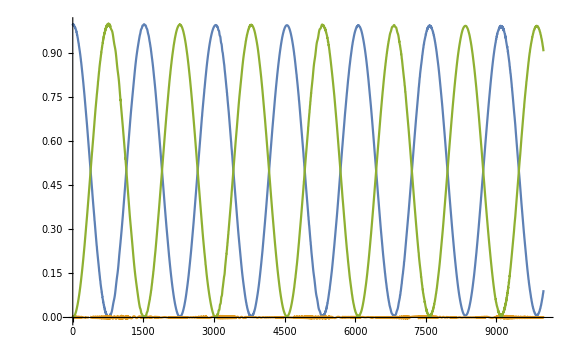

```mathematica
startT = 50;
q2 = 0;
θ2=π/180*0;
q1 = 0;
θ1=π/180*0;
ω1 =ExcE-GroundE;
ω2 =RydE-ExcE;
Ω1=0.443992*2;
Ω2=0.0616463*2;
T11=26.24*10^0;
T12=6.20*10^-4*10^9;
Δ1=(2π*2.1);
Δ2=-(2π*2.1)-0.0145;
Setup[{{GroundE ,5,0,1/2,0,∞,0},{ExcE,6,0,1/2,0,T11,4.227d},{RydE,84,0,1/2,0,T12,(0.017d)/(√(2*1/2+1))}},{1,0,0,0,0,0,0,0,0,0,0,0,0},{{ω1,Ω1/2,q1,on,Δ1,θ1},{ω2,Ω2/2,q2,on,Δ2,θ2}},1]//Quiet;
Eqns={};
For[i=1,i<Dimensions[rho][[1]]+1,i++,For[j=i,j<Dimensions[rho][[1]]+1,j++,{Eqns=Append[Eqns,D[rho[[i,j]],t]==VN[[i,j]]],Eqns=Append[Eqns,rho[[i,j]]==ρsta[[i,j]]/.t->0]}]];
Eqns;
expt={};
Print["Hamiltonian is ", H+EXT//MatrixForm];
(*Print["Time before sim: ",CurrentDate["Instant"]];*)
time=10000;
bbb =CurrentDate["Instant"];
For[i=1,i<(Dimensions[rho][[1]]+1),i++,expt=Append[expt,rho[[i,i]]]];
res=Timing[NDSolve[Eqns,expt,{t,time},AccuracyGoal->5,PrecisionGoal->5]];
Print["Time to run sim: ",res[[1]]];
s = res[[2]];
(*Print["Time after sim: ",CurrentDate["Instant"]];*)
bbc =CurrentDate["Instant"];
(*Print["Time to run simulation:  ",bbc-bbb];*)
plt={};
plt2 = {};
For[i=1,i<(Dimensions[rho][[1]]+1),i++,plt=Append[plt,s[[1]][[i]][[2]]]];
For[i=1,i<(Dimensions[rho][[1]]+1),i++,plt2=Append[plt2,Re[s[[1]][[i]][[2]]]]];
Print[CurrentDate["Instant"]]
Plot[plt,{t,0,time},ImageSize->Large,PlotLegends->Automatic]
```

```mathematica
coupmat//MatrixForm
H//MatrixForm
```

(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)

(0.+0. ⅈ | -0.443992+0. ⅈ | 0.+0. ⅈ
-0.443992+0. ⅈ | -13.1947+0. ⅈ | -0.0616463+0. ⅈ
0.+0. ⅈ | -0.0616463+0. ⅈ | 0.0145+0. ⅈ)

```mathematica
cc = Print[DateObject[Today, "Instant"]](*CurrentDate["Instant"]]*)
preRydReten = AppendTo[preRydReten,plt2[[3]][[Dimensions[plt2[[3]]][[1]]]]/.t->time];
cb = Print[DateObject[Today, "Instant"]](*CurrentDate["Instant"]]*)
Print[cb-cc]
```

DateObject[Mon 4 May 2020,Instant]

DateObject[Mon 4 May 2020,Instant]

0

```mathematica
trans480nmp5µmReten = RydReten;
trans480nmp5µmMA1 = MA780monitor2;
trans480nmp5µmMD1 = MDmonitor2;
(*Mean[HotMA1]
Mean[MA480monitor2]*)
trans480nmp5µmACSE1 = 0;
```

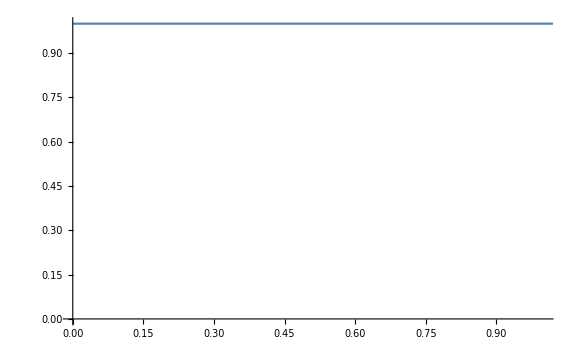

```mathematica
Show[{ListPlot[{trans480nmp5µmReten  },ImageSize->Large,Joined->True,PlotStyle->PointSize[0.01]],Plot[1,{x,0,10000}]}]
(*ListPlot[{HotMD1},ImageSize->Large,Joined->True]
ListPlot[{HotMA1},ImageSize->Large,Joined->True]
ListPlot[{MA480monitor2},ImageSize->Large,Joined->True]*)
```

### testing

```mathematica
Eqns
H//MatrixForm
rho//MatrixForm
EXT//MatrixForm
VN//MatrixForm
```

{ρ⟦1,1⟧'[t]==0.+ⅈ ((0.+0. ⅈ)-(0.443992+0. ⅈ) Conjugate[ρ⟦1,2⟧[t]]+(0.443992+0. ⅈ) ρ⟦1,2⟧[t])+0.0381098 ρ⟦2,2⟧[t]+8.06452×10^-7 ρ⟦3,3⟧[t],ρ⟦1,1⟧[0]==1,ρ⟦1,2⟧'[t]==-0.0190549 ρ⟦1,2⟧[t]+ⅈ ((0.+0. ⅈ)+(0.443992+0. ⅈ) ρ⟦1,1⟧[t]+(13.1947+0. ⅈ) ρ⟦1,2⟧[t]+(0.0616463+0. ⅈ) ρ⟦1,3⟧[t]-(0.443992+0. ⅈ) ρ⟦2,2⟧[t]),ρ⟦1,2⟧[0]==0,ρ⟦1,3⟧'[t]==-8.06452×10^-7 ρ⟦1,3⟧[t]+ⅈ ((0.+0. ⅈ)+(0.0616463+0. ⅈ) ρ⟦1,2⟧[t]-(0.0145+0. ⅈ) ρ⟦1,3⟧[t]-(0.443992+0. ⅈ) ρ⟦2,3⟧[t]),ρ⟦1,3⟧[0]==0,ρ⟦2,2⟧'[t]==0.-0.0381098 ρ⟦2,2⟧[t]+ⅈ ((0.+0. ⅈ)+(0.443992+0. ⅈ) Conjugate[ρ⟦1,2⟧[t]]-(0.0616463+0. ⅈ) Conjugate[ρ⟦2,3⟧[t]]-(0.443992+0. ⅈ) ρ⟦1,2⟧[t]+(0.0616463+0. ⅈ) ρ⟦2,3⟧[t])+8.06452×10^-7 ρ⟦3,3⟧[t],ρ⟦2,2⟧[0]==0,ρ⟦2,3⟧'[t]==-8.06452×10^-7 ρ⟦2,3⟧[t]+ⅈ ((0.+0. ⅈ)-(0.443992+0. ⅈ) ρ⟦1,3⟧[t]+(0.0616463+0. ⅈ) ρ⟦2,2⟧[t]-(13.2092+0. ⅈ) ρ⟦2,3⟧[t]-(0.0616463+0. ⅈ) ρ⟦3,3⟧[t]),ρ⟦2,3⟧[0]==0,ρ⟦3,3⟧'[t]==0.+ⅈ ((0.+0. ⅈ)+(0.0616463+0. ⅈ) Conjugate[ρ⟦2,3⟧[t]]-(0.0616463+0. ⅈ) ρ⟦2,3⟧[t])-1.6129×10^-6 ρ⟦3,3⟧[t],ρ⟦3,3⟧[0]==0}

(0.+0. ⅈ | -0.443992+0. ⅈ | 0.+0. ⅈ
-0.443992+0. ⅈ | -13.1947+0. ⅈ | -0.0616463+0. ⅈ
0.+0. ⅈ | -0.0616463+0. ⅈ | 0.0145+0. ⅈ)

(ρ⟦1,1⟧[t] | ρ⟦1,2⟧[t] | ρ⟦1,3⟧[t]
Conjugate[ρ⟦1,2⟧[t]] | ρ⟦2,2⟧[t] | ρ⟦2,3⟧[t]
Conjugate[ρ⟦1,3⟧[t]] | Conjugate[ρ⟦2,3⟧[t]] | ρ⟦3,3⟧[t])

(0.+0.0381098 ρ⟦2,2⟧[t]+8.06452×10^-7 ρ⟦3,3⟧[t] | -0.0190549 ρ⟦1,2⟧[t] | -8.06452×10^-7 ρ⟦1,3⟧[t]
-0.0190549 Conjugate[ρ⟦1,2⟧[t]] | 0.-0.0381098 ρ⟦2,2⟧[t]+8.06452×10^-7 ρ⟦3,3⟧[t] | -8.06452×10^-7 ρ⟦2,3⟧[t]
-8.06452×10^-7 Conjugate[ρ⟦1,3⟧[t]] | -8.06452×10^-7 Conjugate[ρ⟦2,3⟧[t]] | 0.-1.6129×10^-6 ρ⟦3,3⟧[t])

(0.+ⅈ ((0.+0. ⅈ)-(0.443992+0. ⅈ) Conjugate[ρ⟦1,2⟧[t]]+(0.443992+0. ⅈ) ρ⟦1,2⟧[t])+0.0381098 ρ⟦2,2⟧[t]+8.06452×10^-7 ρ⟦3,3⟧[t] | -0.0190549 ρ⟦1,2⟧[t]+ⅈ ((0.+0. ⅈ)+(0.443992+0. ⅈ) ρ⟦1,1⟧[t]+(13.1947+0. ⅈ) ρ⟦1,2⟧[t]+(0.0616463+0. ⅈ) ρ⟦1,3⟧[t]-(0.443992+0. ⅈ) ρ⟦2,2⟧[t]) | -8.06452×10^-7 ρ⟦1,3⟧[t]+ⅈ ((0.+0. ⅈ)+(0.0616463+0. ⅈ) ρ⟦1,2⟧[t]-(0.0145+0. ⅈ) ρ⟦1,3⟧[t]-(0.443992+0. ⅈ) ρ⟦2,3⟧[t])
-0.0190549 Conjugate[ρ⟦1,2⟧[t]]+ⅈ ((0.+0. ⅈ)-(13.1947+0. ⅈ) Conjugate[ρ⟦1,2⟧[t]]-(0.0616463+0. ⅈ) Conjugate[ρ⟦1,3⟧[t]]-(0.443992+0. ⅈ) ρ⟦1,1⟧[t]+(0.443992+0. ⅈ) ρ⟦2,2⟧[t]) | 0.-0.0381098 ρ⟦2,2⟧[t]+ⅈ ((0.+0. ⅈ)+(0.443992+0. ⅈ) Conjugate[ρ⟦1,2⟧[t]]-(0.0616463+0. ⅈ) Conjugate[ρ⟦2,3⟧[t]]-(0.443992+0. ⅈ) ρ⟦1,2⟧[t]+(0.0616463+0. ⅈ) ρ⟦2,3⟧[t])+8.06452×10^-7 ρ⟦3,3⟧[t] | -8.06452×10^-7 ρ⟦2,3⟧[t]+ⅈ ((0.+0. ⅈ)-(0.443992+0. ⅈ) ρ⟦1,3⟧[t]+(0.0616463+0. ⅈ) ρ⟦2,2⟧[t]-(13.2092+0. ⅈ) ρ⟦2,3⟧[t]-(0.0616463+0. ⅈ) ρ⟦3,3⟧[t])
-8.06452×10^-7 Conjugate[ρ⟦1,3⟧[t]]+ⅈ ((0.+0. ⅈ)-(0.0616463+0. ⅈ) Conjugate[ρ⟦1,2⟧[t]]+(0.0145+0. ⅈ) Conjugate[ρ⟦1,3⟧[t]]+(0.443992+0. ⅈ) Conjugate[ρ⟦2,3⟧[t]]) | -8.06452×10^-7 Conjugate[ρ⟦2,3⟧[t]]+ⅈ ((0.+0. ⅈ)+(0.443992+0. ⅈ) Conjugate[ρ⟦1,3⟧[t]]+(13.2092+0. ⅈ) Conjugate[ρ⟦2,3⟧[t]]-(0.0616463+0. ⅈ) ρ⟦2,2⟧[t]+(0.0616463+0. ⅈ) ρ⟦3,3⟧[t]) | 0.+ⅈ ((0.+0. ⅈ)+(0.0616463+0. ⅈ) Conjugate[ρ⟦2,3⟧[t]]-(0.0616463+0. ⅈ) ρ⟦2,3⟧[t])-1.6129×10^-6 ρ⟦3,3⟧[t])